```mathematica
SetDirectory["D:\\program files\\Wolfram Research\\Mathematica\\7.0\\AddOns\\ExtraPackages\\MadEvent analysis\\parameter_scans\\plots_for_pub"];
Timing[testp=Import["ax_shower2.lhe","Table"];]
```

{6.98884,Null}

```mathematica
Timing[testp2=Import["grv_shower2.lhe","Table"];]
```

{7.16045,Null}

```mathematica
Timing[testp3=Import["rpv_shower2.lhe","Table"];]
```

{8.47085,Null}

```mathematica
Timing[eventListp=ReadME[testp]; ]
```

{0.39,Null}

```mathematica
ClearSystemCache[];Timing[eventListp=ReadME[testp];]
```

{0.39,Null}

```mathematica
Timing[eventListp2=ReadME[testp2]; ]
```

{0.2964,Null}

```mathematica
Timing[eventListp3=ReadME[testp3];]
```

{0.3588,Null}

```mathematica
Nev = Length[eventListp]-1
```

10000

```mathematica
Nev2 = Length[eventListp2]-1
```

10000

```mathematica
Nev3= Length[eventListp3]-1
```

10000

```mathematica
tsp={eventListp[[1]],eventListp2[[1]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
u | in | 0 | 0 | 0 | 0 | 34.6 | -30.2 | 147. | 154. | 0. | 0 | 0
uBar | in | 0 | 0 | 0 | 0 | 2.35 | -3.37 | -2010. | 2010. | 0. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | -168. | -57. | -593. | 788. | 489. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | 205. | 23.4 | -1270. | 1380. | 489. | 0 | 0
particle[9000006] | decayed | 3 | 3 | 0 | 0 | 59.7 | -124. | -74. | 156. | 0. | 0 | 0
d | decayed | 3 | 3 | 0 | 0 | -211. | 6.65 | -528. | 569. | 0. | 0 | 0
dBar | decayed | 3 | 3 | 0 | 0 | -16.6 | 60.3 | 9.73 | 63.3 | 0. | 0 | 0
particle[9000006] | decayed | 4 | 4 | 0 | 0 | 65.2 | -95.1 | -561. | 573. | 0. | 0 | 0
d | decayed | 4 | 4 | 0 | 0 | 187. | 202. | -588. | 649. | 0. | 0 | 0
dBar | decayed | 4 | 4 | 0 | 0 | -47.5 | -83.7 | -123. | 157. | 0. | 0 | 0
particle[9000006] | out | 3 | 3 | 0 | 0 | 59.7 | -124. | -74. | 156. | 0. | 0 | 0
particle[9000006] | out | 4 | 4 | 0 | 0 | 65.2 | -95.1 | -561. | 573. | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 181. | 184. | -548. | 606. | 24.4 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -209. | 6.74 | -528. | 569. | 27. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -40.8 | -61.2 | -56.7 | 93.5 | 10.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -18.9 | 57.8 | 8.04 | 63.6 | 16.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -32.2 | 29. | -47. | 64.6 | 9. | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
uBar | in | 0 | 0 | 0 | 0 | 6.41 | -1.81 | 950. | 950. | 0. | 0 | 0
u | in | 0 | 0 | 0 | 0 | 129. | -134. | -400. | 441. | 0. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | 410. | 98.4 | 149. | 662. | 489. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | -274. | -234. | 401. | 728. | 489. | 0 | 0
particle[1000049] | decayed | 3 | 3 | 0 | 0 | 437. | 147. | -20.6 | 461. | 0. | 0 | 0
s | decayed | 3 | 3 | 0 | 0 | -35.9 | 10.2 | 24.3 | 44.6 | 0. | 0 | 0
sBar | decayed | 3 | 3 | 0 | 0 | 8.97 | -58.5 | 145. | 157. | 0. | 0 | 0
particle[1000049] | decayed | 4 | 4 | 0 | 0 | -170. | 82.6 | -12.1 | 189. | 0. | 0 | 0
c | decayed | 4 | 4 | 0 | 0 | -37.9 | -220. | 226. | 317. | 1.5 | 0 | 0
cBar | decayed | 4 | 4 | 0 | 0 | -66.7 | -97.1 | 188. | 222. | 1.5 | 0 | 0
particle[1000049] | out | 3 | 3 | 0 | 0 | 437. | 147. | -20.6 | 461. | 0. | 0 | 0
particle[1000049] | out | 4 | 4 | 0 | 0 | -170. | 82.6 | -12.1 | 189. | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -99.1 | -317. | 401. | 528. | 91.6 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -118. | 129. | -241. | 299. | 25.8 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 6.21 | -39.2 | 98.4 | 106. | 1.19 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -32.3 | 10.2 | 27.9 | 44.9 | 9.54 | 0 | 0)

```mathematica
eventListOutLp=SetOut[eventListp];
```

```mathematica
eventListOutLp2=SetOut[eventListp2];
```

```mathematica
eventListOutLp3=SetOut[eventListp3];
```

```mathematica
tsp={eventListOutLp[[10000]],eventListOutLp3[[8]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
particle[9000006] | out | 3 | 3 | 0 | 0 | -21.5 | -37.8 | 273. | 277. | 0. | 0 | 0
particle[9000006] | out | 4 | 4 | 0 | 0 | 92.6 | 13.5 | -13.2 | 94.5 | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -491. | 672. | 922. | 1250. | 134. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 356. | -622. | -22.4 | 751. | 224. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 42.6 | -13.7 | 25.8 | 53. | 11.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 8.71 | -27.7 | -19.6 | 36.7 | 10.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 21.5 | 11.2 | -17.4 | 30.5 | 6.14 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -17.6 | -10.1 | -54. | 57.7 | 2.84 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -6.56 | -9.33 | -3.13 | 12.2 | 2.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 8.7 | 6.48 | -558. | 558. | 2.36 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -79.9 | -461. | 112. | 484. | 52.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 175. | 419. | -474. | 657. | 37.2 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -145. | -118. | -10.1 | 188. | 8.77 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 121. | 4.57 | 34.4 | 127. | 20.3 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -57.3 | -35.1 | -113. | 133. | 17. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -1.29 | -12. | -33.6 | 35.8 | 3.32 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -10.7 | -3.37 | 128. | 128. | 4.73 | 0 | 0
⋁_e  | out | 0 | 0 | 0 | 0 | 2.08 | 217. | 0. | 217. | 0. | 0 | 0)

```mathematica
JustTheNeutrinos= {12,_,_,_,_,_,_,_,_,_,_,_,_}  ;
JustTheBs= {5,_,_,_,_,_,_,_,_,_,_,_,_}  ;
JustTheDM={9000006,_,_,_,_,_,_,_,_,_,_,_,_} |{1000049,_,_,_,_,_,_,_,_,_,_,_,_};
RemoveNeutrinos [event_]:=(DeleteCases[event,JustTheNeutrinos,{2}]);
RemoveBs[event_]:=(DeleteCases[event,JustTheBs,{2}]);
RemoveDM[event_]:=(DeleteCases[event,JustTheDM,{2}]);
eventListOutClean=RemoveBs[RemoveNeutrinos[eventListOutLp]];
eventListOutClean2=RemoveBs[RemoveNeutrinos[eventListOutLp2]];
eventListOutClean3=RemoveBs[eventListOutLp3];
eventListOutJets= RemoveDM[eventListOutClean];
eventListOutJets2= RemoveDM[eventListOutClean2];
eventListOutJets3= RemoveNeutrinos[eventListOutClean3];
```

```mathematica
tsp={eventListOutClean[[1]],eventListOutClean3[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
particle[9000006] | out | 3 | 3 | 0 | 0 | 59.7 | -124. | -74. | 156. | 0. | 0 | 0
particle[9000006] | out | 4 | 4 | 0 | 0 | 65.2 | -95.1 | -561. | 573. | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 181. | 184. | -548. | 606. | 24.4 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -209. | 6.74 | -528. | 569. | 27. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -40.8 | -61.2 | -56.7 | 93.5 | 10.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -18.9 | 57.8 | 8.04 | 63.6 | 16.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -32.2 | 29. | -47. | 64.6 | 9. | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -354. | 205. | 5.55 | 413. | 56.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 212. | 34.1 | 1060. | 1080. | 25.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 133. | -4.19 | 197. | 238. | 17.2 | 0 | 0
⋁_e  | out | 0 | 0 | 0 | 0 | 19.9 | -234. | 0. | 235. | 0. | 0 | 0)

```mathematica
tsp={eventListOutJets[[8]],eventListOutJets3[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | 153. | -173. | 1610. | 1630. | 21.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -154. | 24.3 | 718. | 734. | 9.62 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -138. | -6.9 | -111. | 178. | 18.3 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 4. | 60.8 | 46. | 77.5 | 13.5 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -0.695 | 15.9 | -28. | 32.6 | 5.21 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -354. | 205. | 5.55 | 413. | 56.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 212. | 34.1 | 1060. | 1080. | 25.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 133. | -4.19 | 197. | 238. | 17.2 | 0 | 0)

```mathematica
Cuts[event_]:=If[ptOf[event]>40,event];
eventListOutCutJets=Map[Cuts,eventListOutJets,{2}];
eventListOutCutJets=DeleteCases[eventListOutCutJets,Null,2];
eventListOutCutJets2=Map[Cuts,eventListOutJets2,{2}];
eventListOutCutJets2=DeleteCases[eventListOutCutJets2,Null,2];
eventListOutCutJets3=Map[Cuts,eventListOutJets3,{2}];
eventListOutCutJets3=DeleteCases[eventListOutCutJets3,Null,2];

tsp={eventListOutCutJets[[8]],eventListOutCutJets2[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | 153. | -173. | 1610. | 1630. | 21.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -154. | 24.3 | 718. | 734. | 9.62 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -138. | -6.9 | -111. | 178. | 18.3 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 4. | 60.8 | 46. | 77.5 | 13.5 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -299. | -706. | 406. | 872. | 92. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -121. | 441. | 498. | 677. | 21.6 | 0 | 0)

```mathematica
Exactly4Jets={_,_,_,_} ;
Require4Jets[event_]:=(Cases[event,Exactly4Jets,{1}]);
eventList4CutJets= Require4Jets[eventListOutCutJets];
eventList4CutJets2= Require4Jets[eventListOutCutJets2];
eventList4CutJets3= Require4Jets[eventListOutCutJets3];
Jet4Nev = Length[eventList4CutJets]
Jet4Nev2 = Length[eventList4CutJets2]
Jet4Nev3= Length[eventList4CutJets3]
```

3901

1568

4240

```mathematica
Exactly6Jets={_,_,_,_,_,_} ;
Require6Jets[event_]:=(Cases[event,Exactly6Jets,{1}]);
eventList6CutJets= Require6Jets[eventListOutCutJets];
eventList6CutJets2= Require6Jets[eventListOutCutJets2];
eventList6CutJets3= Require6Jets[eventListOutCutJets3];
Jet6Nev = Length[eventList6CutJets]
Jet6Nev2 = Length[eventList6CutJets2]
Jet6Nev3= Length[eventList6CutJets3]
```

539

88

758

```mathematica
tsp={eventList4CutJets[[10]],eventList4CutJets2[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | 377. | -132. | 497. | 645. | 96.3 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -344. | -35. | 269. | 441. | 55.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -58.7 | 6.02 | 1300. | 1300. | 17.4 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 37. | 41.3 | 25.3 | 62.3 | 12.7 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -181. | 434. | 258. | 544. | 89.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 189. | -253. | 354. | 479. | 64.5 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -148. | -136. | 270. | 339. | 35.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -38.3 | -27.1 | -23.2 | 54.7 | 16.1 | 0 | 0)

```mathematica
numJets[event_]:=Length[event];
numJetsPlot = Map[numJets[#] &, eventListOutJets[[1;;Nev]]];
numJetsBGPlot = Map[numJets[#] &, eventListOutJets2[[1;;Nev2]]];
numJetsRPVPlot= Map[numJets[#] &, eventListOutJets3[[1;;Nev3]]];
```

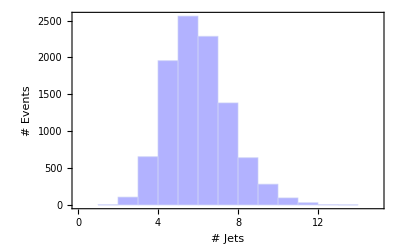

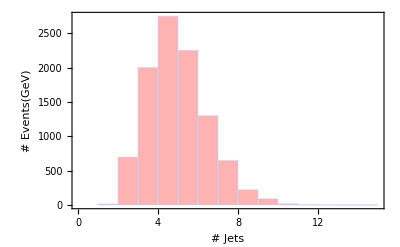

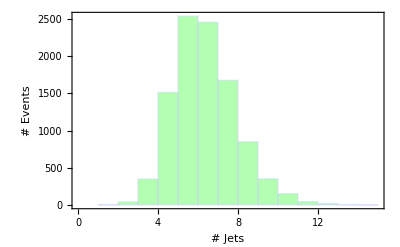

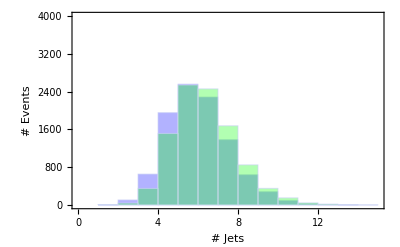

```mathematica
g1=Histogram[numJetsPlot, {0,15,1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events"}]
g2=Histogram[numJetsBGPlot, {0,15,1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events(GeV)"}]
g3=Histogram[numJetsRPVPlot, {0,15,1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events"}]
Show[g1,g3,PlotRange->{{0,15},{0,4000}}]
```

```mathematica
numJets[event_]:=Length[event];
numJetsPlot = Map[numJets[#] &, eventListOutCutJets[[1;;Nev]]];
numJetsBGPlot = Map[numJets[#] &, eventListOutCutJets2[[1;;Nev2]]];
numJetsRPVPlot= Map[numJets[#] &, eventListOutCutJets3[[1;;Nev3]]];
```

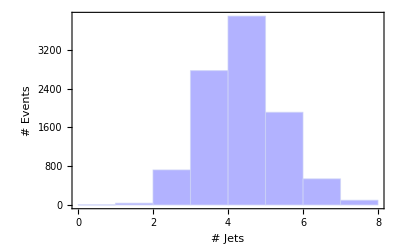

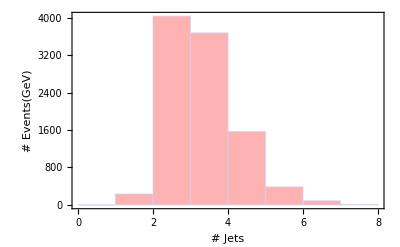

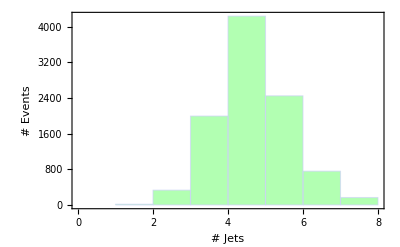

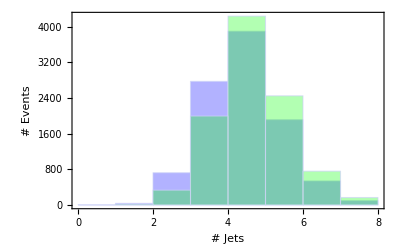

```mathematica
g1=Histogram[numJetsPlot, {0,8,1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events"}]
g2=Histogram[numJetsBGPlot, {0,8,1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events(GeV)"}]
g3=Histogram[numJetsRPVPlot, {0,8,1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events"}]
Show[g1,g3]
```

```mathematica
JetPtTot[event_]:=Total[Map[ptOf[#]&, event],2]
JetPtTotAxPlot = Map[JetPtTot[#] &, eventListOutJets[[1;;Nev]]];
JetPtTotGrvPlot = Map[JetPtTot[#] &, eventListOutJets2[[1;;Nev2]]];
JetPtTotRPVPlot = Map[JetPtTot[#] &, eventListOutJets3[[1;;Nev3]]];
```

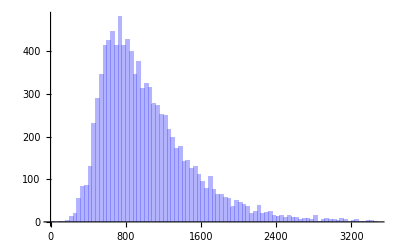

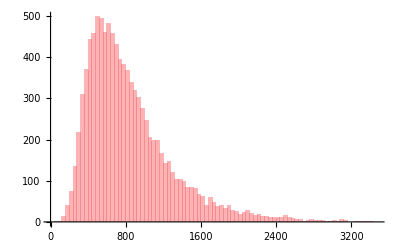

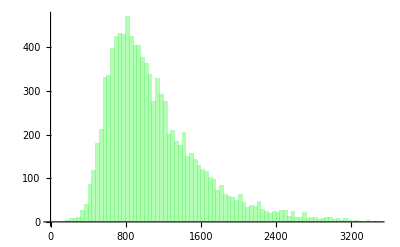

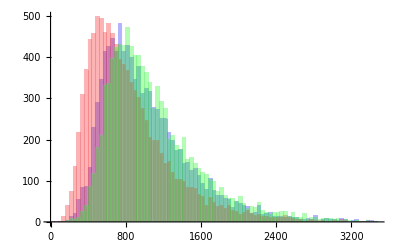

```mathematica
g1=Histogram[JetPtTotAxPlot, {0,3500,40},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[JetPtTotGrvPlot, {0,3500,40},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[JetPtTotRPVPlot, {0,3500,40},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

```mathematica
LeadingEta[event_]:=etaOf[First[PTSort[event]]];
LeadingEtaPlot = Map[LeadingEta[#] &, eventListOutJets[[1;;Nev]]];
LeadingEtaBGPlot = Map[LeadingEta[#] &, eventListOutJets2[[1;;Nev2]]];
LeadingEtaRPVPlot = Map[LeadingEta[#] &, eventListOutJets3[[1;;Nev3]]];
```

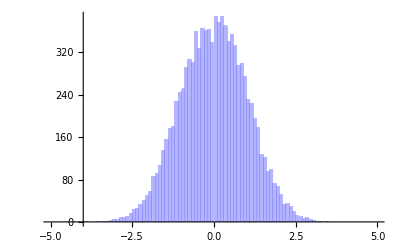

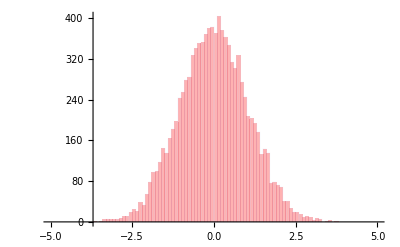

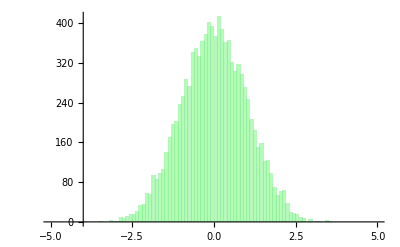

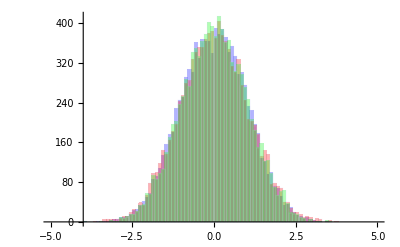

```mathematica
g1=Histogram[LeadingEtaPlot, {-5,5,0.1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
g2=Histogram[LeadingEtaBGPlot, {-5,5,0.1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
g3=Histogram[LeadingEtaRPVPlot, {-5,5,0.1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
Show[g1,g2,g3]
```

```mathematica
InvM1[event_]:=Sqrt[enOf[event[[1]]]*enOf[event[[1]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[1]]]]
InvM2[event_]:=Sqrt[enOf[event[[2]]]*enOf[event[[2]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[2]]]];
InvM3[event_]:=Sqrt[enOf[event[[3]]]*enOf[event[[3]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[3]]]];
InvM4[event_]:=Sqrt[enOf[event[[4]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[4]]].ThreeVectorFrom[event[[4]]]];
InvM12[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[2]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[2]]])];
InvM23[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[2]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[2]]])];
InvM34[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[4]]])];
InvM41[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[4]]])];
InvM31[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[1]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[1]]])];
InvM24[event_] := Sqrt[2*(enOf[event[[2]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[4]]])];
InvM51[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[5]]])];
InvM52[event_] := Sqrt[2*(enOf[event[[2]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[5]]])];
InvM53[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[5]]])];
InvM54[event_] := Sqrt[2*(enOf[event[[4]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[4]]].ThreeVectorFrom[event[[5]]])];
InvM61[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[6]]])];
InvM62[event_] := Sqrt[2*(enOf[event[[2]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[6]]])];
InvM63[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[6]]])];
InvM64[event_] := Sqrt[2*(enOf[event[[4]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[4]]].ThreeVectorFrom[event[[6]]])];
InvM65[event_] := Sqrt[2*(enOf[event[[5]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[5]]].ThreeVectorFrom[event[[6]]])];
InvM123[event_] := Sqrt[(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[3]]])*(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[3]]])-(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]]).(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]])];
InvM124[event_] := Sqrt[(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[4]]])*(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[4]]])-(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[4]]]).(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[4]]])];
InvM423[event_] := Sqrt[(enOf[event[[4]]]+enOf[event[[2]]]+enOf[event[[3]]])*(enOf[event[[4]]]+enOf[event[[2]]]+enOf[event[[3]]])-(ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]]).(ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]])];
InvM143[event_] := Sqrt[(enOf[event[[1]]]+enOf[event[[4]]]+enOf[event[[3]]])*(enOf[event[[1]]]+enOf[event[[4]]]+enOf[event[[3]]])-(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[3]]]).(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[3]]])];

ResDiffList[event_]:={Abs[InvM12[event]-InvM34[event]],Abs[InvM23[event]-InvM41[event]],Abs[InvM31[event]-InvM24[event]],Abs[InvM123[event]-InvM4[event]],Abs[InvM124[event]-InvM3[event]],Abs[InvM423[event]-InvM1[event]],Abs[InvM143[event]-InvM2[event]]}

ReducedInvMass[event_]:=Which[
Min[ResDiffList[event]]==Abs[InvM12[event]-InvM34[event]],InvM12[event],
Min[ResDiffList[event]]==Abs[InvM23[event]-InvM41[event]],InvM23[event],
Min[ResDiffList[event]]==Abs[InvM31[event]-InvM24[event]],InvM31[event],
Min[ResDiffList[event]]==Abs[InvM123[event]-InvM4[event]],InvM123[event],
Min[ResDiffList[event]]==Abs[InvM124[event]-InvM3[event]],InvM124[event],
Min[ResDiffList[event]]==Abs[InvM423[event]-InvM1[event]],InvM423[event],
Min[ResDiffList[event]]==Abs[InvM143[event]-InvM2[event]],InvM143[event]
];
```

```mathematica
ReduceJetInvMassPlot = Map[ReducedInvMass[#] &, eventList4CutJets[[1;;Jet4Nev]]];
ReducedJetInvMassBGPlot = Map[ReducedInvMass[#] &, eventList4CutJets2[[1;;Jet4Nev2]]];
ReducedJetInvMassRPVPlot = Map[ReducedInvMass[#] &, eventList4CutJets3[[1;;Jet4Nev3]]];
```

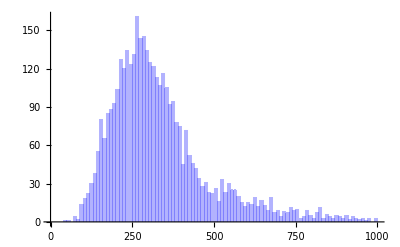

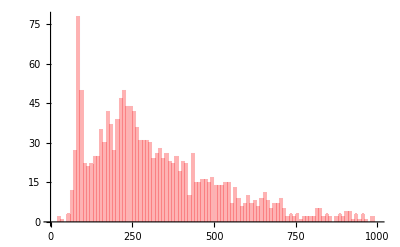

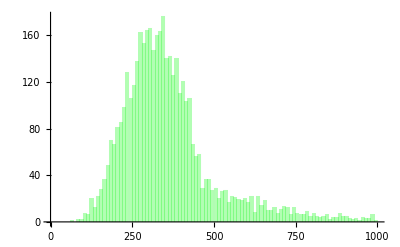

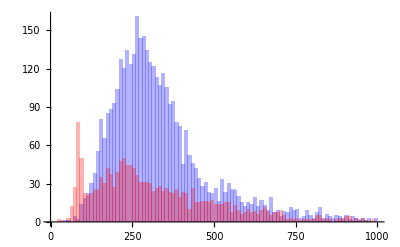

```mathematica
g1=Histogram[ReduceJetInvMassPlot, {0,1000,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[ReducedJetInvMassBGPlot, {0,1000,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[ReducedJetInvMassRPVPlot, {0,1000,10},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

```mathematica
AllInvMassPlot=Flatten[{Map[InvM12[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM23[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM34[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM41[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM31[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM24[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM123[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM124[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM423[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM143[#]&,eventList4CutJets[[1;;Jet4Nev]]]},1];
AllInvMassBGPlot=Flatten[{Map[InvM12[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM23[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM34[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM41[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM31[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM24[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM123[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM124[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM423[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM143[#]&,eventList4CutJets2[[1;;Jet4Nev2]]]},1];
AllInvMassRPVPlot=Flatten[{Map[InvM12[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM23[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM34[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM41[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM31[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM24[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM123[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM124[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM423[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM143[#]&,eventList4CutJets3[[1;;Jet4Nev3]]]},1];
Length[AllInvMassPlot]
```

39010

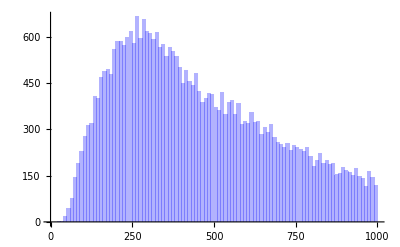

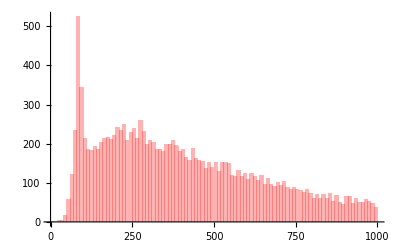

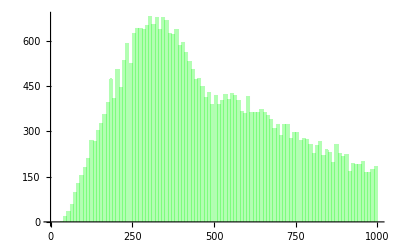

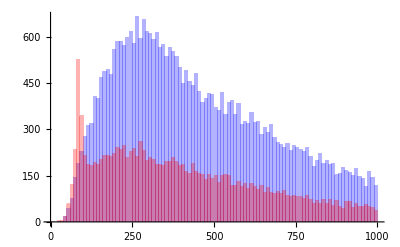

```mathematica
g1=Histogram[AllInvMassPlot, {0,1000,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[AllInvMassBGPlot, {0,1000,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[AllInvMassRPVPlot, {0,1000,10},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

```mathematica
ZDiffList[event_]:={Abs[InvM12[event]-90],Abs[InvM23[event]-90],Abs[InvM34[event]-90],Abs[InvM41[event]-90],Abs[InvM31[event]-90],Abs[InvM24[event]-90],Abs[InvM123[event]-90],Abs[InvM124[event]-90],Abs[InvM423[event]-90],Abs[InvM143[event]-90]}
```

```mathematica
ZFilterInvMass[event_]:=Which[
Min[ZDiffList[event]]==Abs[InvM12[event]-90],InvM12[event],
Min[ZDiffList[event]]==Abs[InvM23[event]-90],InvM23[event],
Min[ZDiffList[event]]==Abs[InvM34[event]-90],InvM34[event],
Min[ZDiffList[event]]==Abs[InvM41[event]-90],InvM41[event],
Min[ZDiffList[event]]==Abs[InvM24[event]-90],InvM24[event],
Min[ZDiffList[event]]==Abs[InvM31[event]-90],InvM31[event],
Min[ZDiffList[event]]==Abs[InvM123[event]-90],InvM123[event],
Min[ZDiffList[event]]==Abs[InvM124[event]-90],InvM124[event],
Min[ZDiffList[event]]==Abs[InvM423[event]-90],InvM423[event],
Min[ZDiffList[event]]==Abs[InvM143[event]-90],InvM143[event]
];
ZFilterInvMassPlot = Flatten[Map[ZFilterInvMass[#] &, eventList4CutJets[[1;;Jet4Nev]]]];
ZFilterInvMassBGPlot = Flatten[Map[ZFilterInvMass[#] &, eventList4CutJets2[[1;;Jet4Nev2]]]];
ZFilterInvMassRPVPlot = Flatten[Map[ZFilterInvMass[#] &, eventList4CutJets3[[1;;Jet4Nev3]]]];
Length[ZFilterInvMassPlot]
```

3901

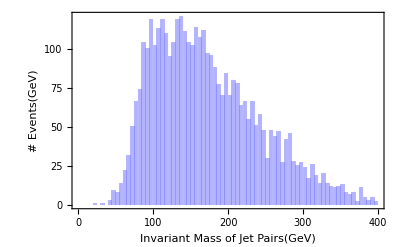

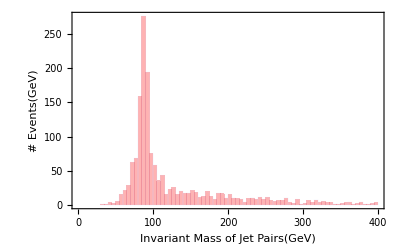

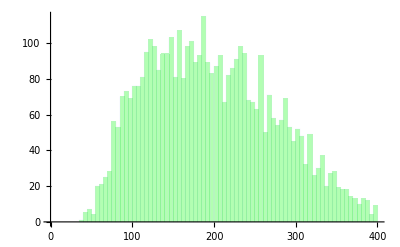

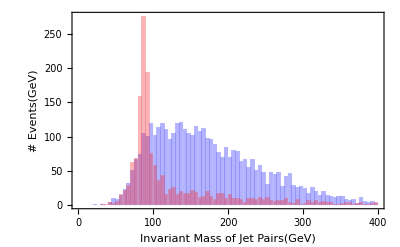

```mathematica
g1=Histogram[ZFilterInvMassPlot, {0,400,5},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"Invariant Mass of Jet Pairs(GeV)","# Events(GeV)"}]
g2=Histogram[ZFilterInvMassBGPlot,{0,400,5},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},AxesOrigin->{0,0},AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"Invariant Mass of Jet Pairs(GeV)","# Events(GeV)"}]
g3=Histogram[ZFilterInvMassRPVPlot,{0,400,5},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

```mathematica
AllInvMassPairsPlot=Flatten[{Map[InvM12[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM23[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM34[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM41[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM31[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM24[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM51[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM52[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM53[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM54[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM61[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM62[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM63[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM64[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM65[#]&,eventList6CutJets[[1;;Jet6Nev]]]},1];
AllInvMassPairsBGPlot=Flatten[{Map[InvM12[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM23[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM34[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM41[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM31[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM24[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM51[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM52[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM53[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM54[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM61[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM62[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM63[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM64[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM65[#]&,eventList6CutJets2[[1;;Jet6Nev2]]]},1];
AllInvMassPairsRPVPlot=Flatten[{Map[InvM12[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM23[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM34[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM41[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM31[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM24[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM51[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM52[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM53[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM54[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM61[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM62[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM63[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM64[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM65[#]&,eventList6CutJets3[[1;;Jet6Nev3]]]},1];
```

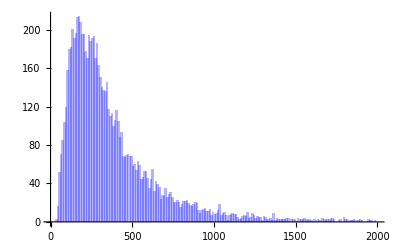

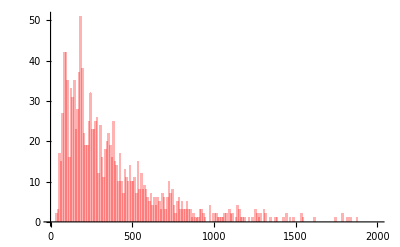

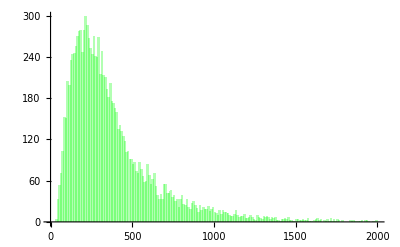

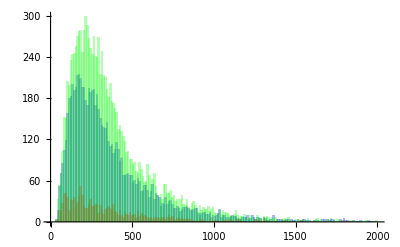

```mathematica
g1=Histogram[AllInvMassPairsPlot, {0,2000,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[AllInvMassPairsBGPlot, {0,2000,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[AllInvMassPairsRPVPlot, {0,2000,10},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

```mathematica
MHT[event_]:=Abs[√((-Total[Map[pxOf,event,{1}]])^2+(-Total[Map[pxOf,event,{1}]])^2)];
```

```mathematica
MHTPlot = Map[MHT[#] &, eventListOutCutJets[[1;;Nev]]];
MHTBGPlot = Map[MHT[#] &, eventListOutCutJets2[[1;;Nev2]]];
MHTLVPlot = Map[MHT[#] &, eventListOutCutJets3[[1;;Nev2]]];
```

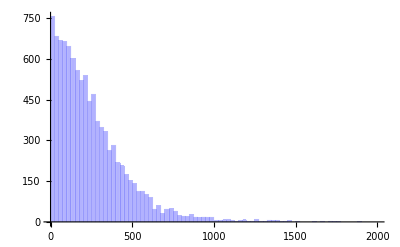

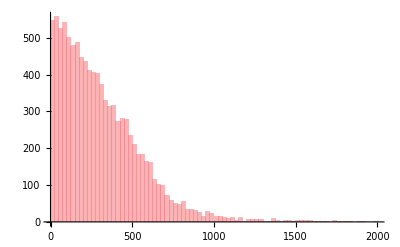

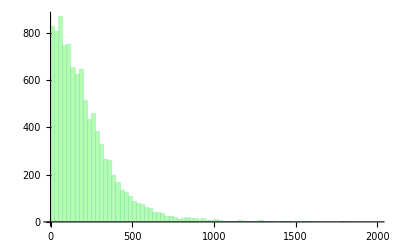

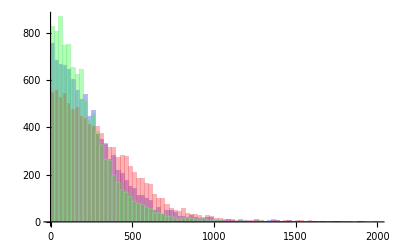

```mathematica
h1=Histogram[MHTPlot, {0,2000,25},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
h2=Histogram[MHTBGPlot, {0,2000,25},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
h4=Histogram[MHTLVPlot, {0,2000,25},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[h1,h2,h4]
```

```mathematica
HtvsMETAxdata=Transpose@{JetPtTotAxPlot,ptmissAxPlot};
HtvsMETGrvdata=Transpose@{JetPtTotGrvPlot,ptmissGrvPlot};
HtvsMETRPVdata=Transpose@{JetPtTotRPVPlot,ptmissRPVPlot};

g1=ListPlot[HtvsMETAxdata]
g2=ListPlot[HtvsMETGrvdata,PlotStyle->Red]
g3 =ListPlot[HtvsMETRPVdata,PlotStyle->Green]
Show[g1,g2,g3]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{644.91, 2826.3, 696.617, 639.678, 531.543, 1056.48, 745.948, 601.875, 1050.71, 830.397, 427.985, 585.456, 706.072, 859.734, 738.68, 1509.6, 920.837, 646.163, « 16 », 595.476, 910.319, 800.155, 1638.42, 729.491, 1158.45, 1006.33, 894.091, 540.003, 801.203, 798.424, 900.774, 731.896, 1282.35, 654.788, 1429.15, « 9950 »}, ptmissAxPlot} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{580.519, 948.399, 513.514, 974.001, 617.121, 192.058, 273.05, 755.058, 679.636, 652.448, 559.943, 457.519, 569.38, 707.812, 626.347, 638.347, 779.386, 1089.79, « 16 », 696.547, 338.625, 329.523, 841.776, 724.911, 878.598, 516.288, 652.029, 940.603, 452.958, 825.773, 445.063, 476.539, 327.773, 1113.64, 1977.31, « 9950 »}, ptmissGrvPlot} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{990.618, 1296.81, 643.029, 530.37, 949.233, 1491.24, 897.228, 1320.47, 736.197, 456.673, 760.767, 829.951, 1032.56, 858.427, 496.007, 1109.07, 879.081, 1638.24, « 16 », 781.835, 1252.27, 2209.81, 1833.64, 535.618, 1060.53, 2872.87, 758.919, 1598.76, 1085.27, 682.915, 1427.37, 1832.79, 1621.6, 579.191, 624.278, « 9950 »}, « 13 »} cannot be transposed.

ListPlot::lpn: Transpose[{{644.91, 2826.3, 696.617, 639.678, 531.543, 1056.48, 745.948, 601.875, 1050.71, 830.397, 427.985, 585.456, 706.072, 859.734, 738.68, 1509.6, 920.837, « 17 », 595.476, 910.319, 800.155, 1638.42, 729.491, 1158.45, 1006.33, 894.091, 540.003, 801.203, 798.424, 900.774, 731.896, 1282.35, 654.788, 1429.15, « 9950 »}, ptmissAxPlot}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{644.91,2826.3,696.617,639.678,531.543,1056.48,745.948,601.875,1050.71,830.397,427.985,585.456,706.072,859.734,738.68,1509.6,920.837,«9967»,1024.54,2168.01,960.367,440.233,1375.32,1321.47,925.995,553.227,1062.13,1645.95,1697.23,706.786,1556.25,1359.98,475.552,1689.51},«12»}]]

ListPlot::lpn: Transpose[{{580.519, 948.399, 513.514, 974.001, 617.121, 192.058, 273.05, 755.058, 679.636, 652.448, 559.943, 457.519, 569.38, 707.812, 626.347, 638.347, 779.386, « 17 », 696.547, 338.625, 329.523, 841.776, 724.911, 878.598, 516.288, 652.029, 940.603, 452.958, 825.773, 445.063, 476.539, 327.773, 1113.64, 1977.31, « 9950 »}, ptmissGrvPlot}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{580.519,948.399,513.514,974.001,617.121,192.058,273.05,755.058,679.636,652.448,559.943,457.519,569.38,707.812,626.347,638.347,779.386,«9967»,968.426,403.59,356.104,451.008,735.838,688.261,509.814,763.725,323.063,163.087,1123.66,1127.8,719.846,392.823,1330.33,916.683},ptmissGrvPlot}],«1»]

ListPlot::lpn: Transpose[{{990.618, 1296.81, 643.029, 530.37, 949.233, 1491.24, 897.228, 1320.47, 736.197, 456.673, 760.767, 829.951, 1032.56, 858.427, 496.007, 1109.07, 879.081, « 17 », 781.835, 1252.27, 2209.81, 1833.64, 535.618, 1060.53, 2872.87, 758.919, 1598.76, 1085.27, 682.915, 1427.37, 1832.79, 1621.6, 579.191, 624.278, « 9950 »}, ptmissRPVPlot}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{990.618,1296.81,643.029,530.37,949.233,1491.24,897.228,1320.47,736.197,456.673,760.767,829.951,1032.56,858.427,496.007,1109.07,879.081,«9967»,882.511,2711.36,820.091,1137.04,881.296,640.436,643.422,2575.99,642.832,699.428,661.111,1455.45,1678.74,1426.51,2405.27,1222.54},«13»}],«9»→«1»]

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[Transpose[{{644.91,2826.3,696.617,639.678,531.543,1056.48,745.948,601.875,1050.71,830.397,427.985,585.456,706.072,859.734,738.68,1509.6,«9968»,1024.54,2168.01,960.367,440.233,1375.32,1321.47,925.995,553.227,1062.13,1645.95,1697.23,706.786,1556.25,1359.98,475.552,1689.51},ptmissAxPlot}]],«1»,«8»[«1»]]